```mathematica
(*Input path to data file*)
filedir="/home/daneel/workspace/pairing-symmetry/swave/result/";
phikfilename="2dlattice_omega_.10000000_mu_0.01_muamp_-0.1_gsize_144_periods_t_phik_BCS_gnd_swave.dat";
phikfile=StringJoin[filedir,phikfilename];
(*Subscript[u, k]= ϕ[0] + I ϕ[2]*)
(*Subscript[v, k] = ϕ[1] + I ϕ[3]*)
(******************************** t ******* Subscript[k, x] ***** Subscript[k, y] **** ϕ[0] *** ϕ[1] **** ϕ[2] **** ϕ[3] **** Subscript[ρ, d](k) ***Subscript[E, r](k) ****)
ρ=BinaryReadList[phikfile,{"Real64","Real64","Real64","Real64","Real64","Real64","Real64","Real64","Real64"}];
ρ=Select[ρ, #[[2]]≠0&&#[[3]]≠0&&#[[4]]≠0&&#[[5]]≠0&&#[[6]]≠0&&#[[7]]≠0&&#[[8]]≠0&];(*Remove redundant entries*)
(*Drop off the ϕs and Subscript[E, r] s*)
ρ=Drop[ρ,None,{4,7}];
ρ=Drop[ρ,None,{5}];
ρ=GatherBy[ρ,First];(*Gather data by time*)
(*ρ[[i]] is now a list of {t,Subscript[k, x],Subscript[k, y],ρ}... objects *)
```

```mathematica
(*Now, group the momenta only in a matrix*)
k=Take[ρ[[1]],All,{2,3}];
rhoavg=Table[Take[ρ[[i]],All,{4}]//Flatten,{i,1,Length[ρ]}]//Mean;
meandata=Partition[Transpose[{k,rhoavg}]//Flatten,3];
ListPlot3D[meandata]
rhoplot=ListDensityPlot[meandata,ColorFunction->"GrayTones",FrameTicks->None,Background->Black,FrameLabel->{"ω/Δ_0=2.00",None,None,None},TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 20,FontColor->White}]
```

{1.0001,0.0219692,2.70221,0.298692}

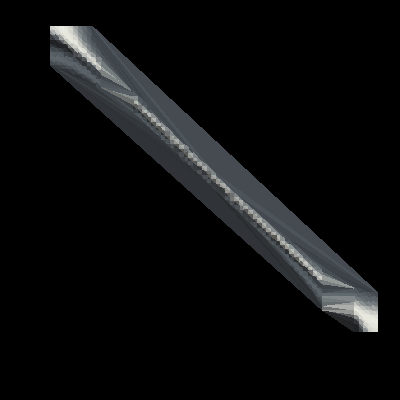

-Graphics3D-

```mathematica
(*Choose a time index by trial and error*)
tindex=4951;
ρ[[tindex]][[1]]
rhot=Drop[ρ[[tindex]],None,{1}];
rhotplot=ListDensityPlot[rhot,ColorFunction->"GrayTones",FrameTicks->None,Background->Black,FrameLabel->{"ω/Δ_0=1.0",None,None,None},TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 20,FontColor->White}]
ListPlot3D[rhot]
```

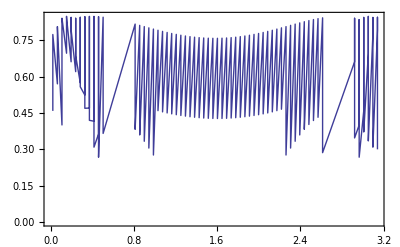

/home/daneel/swave_0.1.dat

```mathematica
mu0=0.01;
tol=0.00001;
kxdata=Select[rhot,Cos[#[[1]]]+Cos[#[[2]]]-mu0≤tol &];
ListPlot[Drop[kxdata,None,{2}],Joined->True,Frame->True,Axes-> False]
Export["/home/daneel/swave_0.1.dat",Drop[kxdata,None,{2}],"Table"]
```